#### 1D chain model

#### Exact diagonalization and exact theoretical solution

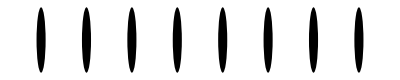

```mathematica
n=8;(* number of the chain sites *)
Chain=Graphics[Table[Disk[{i,0},0.1],{i,1,n}]]
```

```mathematica
(* Generate Hamiltonian matrix of size n x n *)
h[n_]:=Table[If[i==j,2,If[Abs[i-j]==1,-1,0]],{i,1,n},{j,1,n}];
```

```mathematica
h[n]//MatrixForm
```

(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2)

```mathematica
(* Find numerically the eigenvalues of H *)
eigs=Eigenvalues[h[n]//N]
```

{3.87939,3.53209,3.,2.3473,1.6527,1.,0.467911,0.120615}

```mathematica
(* Find numerically the eigenvectors of H *)
vec=Eigenvectors[h[n]//N];
```

```mathematica
(* check *)
h[n].vec[[1]]-eigs[[1]]*vec[[1]]
```

{-3.33067×10^-16,0.,6.66134×10^-16,1.33227×10^-15,0.,-2.22045×10^-16,4.44089×10^-16,3.33067×10^-16}

```mathematica
(* Exact spectrum *)
eExact[k_]:=4 Sin[(π k)/(2(n+1))]^2;
(* Exact eigenvectors *)
vExact[k_]:=Table[Sin[(π k)/(n+1)*i],{i,1,n}]
```

```mathematica
(* Check *)
h.vExact[5]-eExact[5]*vExact[5]//FullSimplify
```

{0,0,0,0,0,0,0,0}

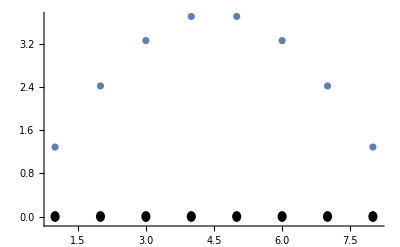

```mathematica
(* Plot of the eigenvectors *)
Show[ListPlot[n*v[[8]]],Chain,PlotRange->All]
```

```mathematica
(* Exact spectrum *)
Exactspec=Table[eExact[k],{k,1,n}]//N
```

{0.120615,0.467911,1.,1.6527,2.3473,3.,3.53209,3.87939}

#### Naive RG approach step by step for better understanding of the process

```mathematica
(* Step 1: initial blocks are just numbers *)
H[1]=2.0;
T[1]=-1.0;
```

```mathematica
(* Step 2: create a bigger blocks *)
H[2]={{H[1],T[1]},{T[1],H[1]}}//N;
T[2]={{0,0},{T[1],0}}//N;
```

```mathematica
{H[2]//MatrixForm,T[2]//MatrixForm}
```

{(2. | -1.
-1. | 2.),(0. | 0.
-1. | 0.)}

```mathematica
(* Eigenvalues and eigenvectors of the Hamiltonian H[2] *)
esys[2]=Eigensystem[H[2]]
```

{{3.,1.},{{-0.707107,0.707107},{-0.707107,-0.707107}}}

```mathematica
(* positions of the sorted eigenvalues *)
pos[2]=Ordering[esys[2][[1]]]
```

{2,1}

```mathematica
(* sorted eigenvalues *)
e[2]=esys[2][[1,pos[2]]]
```

{1.,3.}

```mathematica
(* sorted eigenvectors: each column is an eigenvector *)
v[2]=Transpose[esys[2][[2,pos[2]]]]
```

{{-0.707107,-0.707107},{-0.707107,0.707107}}

```mathematica
(* check *)
H[2].v[2][[;;,1]]-e[2][[1]]*v[2][[;;,1]]
```

{0.,0.}

```mathematica
(* perform a change of basis *)
Hb[2]=v[2]†.H[2].v[2];
Tb[2]=v[2]†.T[2].v[2];
```

```mathematica
{Hb[2]//MatrixForm,Tb[2]//MatrixForm}
```

{(1. | 0.
0. | 3.),(-0.5 | -0.5
0.5 | 0.5)}

```mathematica
(* Step 3: create a bigger blocks *)
H[3]={{Hb[2],Tb[2]},{Tb[2]†,Hb[2]}}//ArrayFlatten;
Zr[2]=ConstantArray[0,{2,2}];
T[3]={{Zr[2],Zr[2]},{Tb[2],Zr[2]}}//ArrayFlatten;
```

```mathematica
{H[3]//MatrixForm,T[3]//MatrixForm}
```

{(1. | 0. | -0.5 | -0.5
0. | 3. | 0.5 | 0.5
-0.5 | 0.5 | 1. | 0.
-0.5 | 0.5 | 0. | 3.),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
-0.5 | -0.5 | 0 | 0
0.5 | 0.5 | 0 | 0)}

```mathematica
(* Eigenvalues and eigenvectors of the Hamiltonian H[3] *)
esys[3]=Eigensystem[H[3]];
```

```mathematica
(* positions of the sorted eigenvalues *)
pos[3]=Ordering[esys[3][[1]]];
```

```mathematica
(* sorted eigenvalues *)
e[3]=esys[3][[1,pos[3]]];
```

```mathematica
(* sorted eigenvectors *)
v[3]=Transpose[esys[3][[2,pos[3]]]];
```

```mathematica
(* check *)
H[3].v[3][[;;,2]]-e[3][[2]]*v[3][[;;,2]];
```

```mathematica
(* perform a change of basis *)
Hb[3]=v[3]†.H[3].v[3]//Chop;
Tb[3]=v[3]†.T[3].v[3];
```

```mathematica
{Hb[3]//MatrixForm,Tb[3]//MatrixForm}
```

{(0.381966 | 0 | 0 | 0
0 | 1.38197 | 0 | 0
0 | 0 | 2.61803 | 0
0 | 0 | 0 | 3.61803),(-0.138197 | 0.223607 | 0.223607 | 0.138197
-0.223607 | 0.361803 | 0.361803 | 0.223607
0.223607 | -0.361803 | -0.361803 | -0.223607
-0.138197 | 0.223607 | 0.223607 | 0.138197)}

```mathematica
(* Step 4: create a bigger blocks and start truncation *)
H[4]={{Hb[3],Tb[3]},{Tb[3]†,Hb[3]}}//ArrayFlatten;
Zr[3]=ConstantArray[0,{4,4}];
T[4]={{Zr[3],Zr[3]},{Tb[3],Zr[3]}}//ArrayFlatten;
```

```mathematica
{H[4]//MatrixForm,T[4]//MatrixForm}
```

{(0.381966 | 0 | 0 | 0 | -0.138197 | 0.223607 | 0.223607 | 0.138197
0 | 1.38197 | 0 | 0 | -0.223607 | 0.361803 | 0.361803 | 0.223607
0 | 0 | 2.61803 | 0 | 0.223607 | -0.361803 | -0.361803 | -0.223607
0 | 0 | 0 | 3.61803 | -0.138197 | 0.223607 | 0.223607 | 0.138197
-0.138197 | -0.223607 | 0.223607 | -0.138197 | 0.381966 | 0 | 0 | 0
0.223607 | 0.361803 | -0.361803 | 0.223607 | 0 | 1.38197 | 0 | 0
0.223607 | 0.361803 | -0.361803 | 0.223607 | 0 | 0 | 2.61803 | 0
0.138197 | 0.223607 | -0.223607 | 0.138197 | 0 | 0 | 0 | 3.61803),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.138197 | 0.223607 | 0.223607 | 0.138197 | 0 | 0 | 0 | 0
-0.223607 | 0.361803 | 0.361803 | 0.223607 | 0 | 0 | 0 | 0
0.223607 | -0.361803 | -0.361803 | -0.223607 | 0 | 0 | 0 | 0
-0.138197 | 0.223607 | 0.223607 | 0.138197 | 0 | 0 | 0 | 0)}

```mathematica
(* Eigenvalues and eigenvectors of the Hamiltonian H[4] *)
esys[4]=Eigensystem[H[4]];
(* positions of the sorted eigenvalues *)
pos[4]=Ordering[esys[4][[1]]];
(* sorted eigenvalues *)
e[4]=esys[4][[1,pos[4]]];
(* sorted eigenvectors *)
v[4]=Transpose[esys[4][[2,pos[4]]]];
```

```mathematica
(* perform a change of basis *)
Hb[4]=v[4]†.H[4].v[4]//Chop;
Tb[4]=v[4]†.T[4].v[4];
```

```mathematica
{Hb[4]//MatrixForm,Tb[4]//MatrixForm}
```

{(0.120615 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.467911 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.6527 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2.3473 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.53209 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.87939),(-0.0259951 | -0.0488547 | -0.0658218 | 0.0748498 | -0.0748498 | -0.0658218 | -0.0488547 | -0.0259951
0.0488547 | 0.0918169 | 0.123705 | -0.140672 | 0.140672 | 0.123705 | 0.0918169 | 0.0488547
-0.0658218 | -0.123705 | -0.166667 | 0.189526 | -0.189526 | -0.166667 | -0.123705 | -0.0658218
-0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526 | -0.140672 | -0.0748498
-0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526 | -0.140672 | -0.0748498
0.0658218 | 0.123705 | 0.166667 | -0.189526 | 0.189526 | 0.166667 | 0.123705 | 0.0658218
-0.0488547 | -0.0918169 | -0.123705 | 0.140672 | -0.140672 | -0.123705 | -0.0918169 | -0.0488547
0.0259951 | 0.0488547 | 0.0658218 | -0.0748498 | 0.0748498 | 0.0658218 | 0.0488547 | 0.0259951)}

```mathematica
(* Truncation: Take only m lowest energy eigenvectors *)
m=6;
```

```mathematica
v[4][[;;,1;;m]]//MatrixForm
```

(0.660343 | 0.697386 | 0.245562 | 0.088645 | -0.0573158 | 0.0579693
0.221384 | -0.106099 | -0.642889 | 0.673207 | -0.188809 | 0.151765
-0.111812 | 0.0451044 | 0.151765 | 0.188809 | -0.673207 | -0.642889
0.0493453 | -0.0190268 | -0.0579693 | -0.0573158 | 0.088645 | -0.245562
0.660343 | -0.697386 | 0.245562 | -0.088645 | -0.0573158 | -0.0579693
-0.221384 | -0.106099 | 0.642889 | 0.673207 | 0.188809 | 0.151765
-0.111812 | -0.0451044 | 0.151765 | -0.188809 | -0.673207 | 0.642889
-0.0493453 | -0.0190268 | 0.0579693 | -0.0573158 | -0.088645 | -0.245562)

```mathematica
(* perform a change of basis with truncation *)
Hb[4]=v[4][[;;,1;;m]]†.H[4].v[4][[;;,1;;m]]//Chop;
Tb[4]=v[4][[;;,1;;m]]†.T[4].v[4][[;;,1;;m]];
```

```mathematica
{Hb[4]//MatrixForm,Tb[4]//MatrixForm}
```

{(0.120615 | 0 | 0 | 0 | 0 | 0
0 | 0.467911 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1.6527 | 0 | 0
0 | 0 | 0 | 0 | 2.3473 | 0
0 | 0 | 0 | 0 | 0 | 3.),(-0.0259951 | -0.0488547 | -0.0658218 | 0.0748498 | -0.0748498 | -0.0658218
0.0488547 | 0.0918169 | 0.123705 | -0.140672 | 0.140672 | 0.123705
-0.0658218 | -0.123705 | -0.166667 | 0.189526 | -0.189526 | -0.166667
-0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526
-0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526
0.0658218 | 0.123705 | 0.166667 | -0.189526 | 0.189526 | 0.166667)}

```mathematica
(* Step 5: create a bigger blocks *)
H[5]={{Hb[4],Tb[4]},{Tb[4]†,Hb[4]}}//ArrayFlatten;
Zr[4]=ConstantArray[0,{m,m}];
T[5]={{Zr[4],Zr[4]},{Tb[4],Zr[4]}}//ArrayFlatten;
```

```mathematica
{H[5]//MatrixForm,T[5]//MatrixForm}
```

{(0.120615 | 0 | 0 | 0 | 0 | 0 | -0.0259951 | -0.0488547 | -0.0658218 | 0.0748498 | -0.0748498 | -0.0658218
0 | 0.467911 | 0 | 0 | 0 | 0 | 0.0488547 | 0.0918169 | 0.123705 | -0.140672 | 0.140672 | 0.123705
0 | 0 | 1. | 0 | 0 | 0 | -0.0658218 | -0.123705 | -0.166667 | 0.189526 | -0.189526 | -0.166667
0 | 0 | 0 | 1.6527 | 0 | 0 | -0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526
0 | 0 | 0 | 0 | 2.3473 | 0 | -0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526
0 | 0 | 0 | 0 | 0 | 3. | 0.0658218 | 0.123705 | 0.166667 | -0.189526 | 0.189526 | 0.166667
-0.0259951 | 0.0488547 | -0.0658218 | -0.0748498 | -0.0748498 | 0.0658218 | 0.120615 | 0 | 0 | 0 | 0 | 0
-0.0488547 | 0.0918169 | -0.123705 | -0.140672 | -0.140672 | 0.123705 | 0 | 0.467911 | 0 | 0 | 0 | 0
-0.0658218 | 0.123705 | -0.166667 | -0.189526 | -0.189526 | 0.166667 | 0 | 0 | 1. | 0 | 0 | 0
0.0748498 | -0.140672 | 0.189526 | 0.215521 | 0.215521 | -0.189526 | 0 | 0 | 0 | 1.6527 | 0 | 0
-0.0748498 | 0.140672 | -0.189526 | -0.215521 | -0.215521 | 0.189526 | 0 | 0 | 0 | 0 | 2.3473 | 0
-0.0658218 | 0.123705 | -0.166667 | -0.189526 | -0.189526 | 0.166667 | 0 | 0 | 0 | 0 | 0 | 3.),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0259951 | -0.0488547 | -0.0658218 | 0.0748498 | -0.0748498 | -0.0658218 | 0 | 0 | 0 | 0 | 0 | 0
0.0488547 | 0.0918169 | 0.123705 | -0.140672 | 0.140672 | 0.123705 | 0 | 0 | 0 | 0 | 0 | 0
-0.0658218 | -0.123705 | -0.166667 | 0.189526 | -0.189526 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0
-0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526 | 0 | 0 | 0 | 0 | 0 | 0
-0.0748498 | -0.140672 | -0.189526 | 0.215521 | -0.215521 | -0.189526 | 0 | 0 | 0 | 0 | 0 | 0
0.0658218 | 0.123705 | 0.166667 | -0.189526 | 0.189526 | 0.166667 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
Sort[Eigenvalues[H[5]]]
```

{0.0412282,0.135331,0.307142,0.523182,0.802465,1.11169,1.46067,1.82282,2.1931,2.56569,2.90173,3.312}

```mathematica
Sort[Eigenvalues[h[16]//N]]
```

{0.0340538,0.135056,0.299566,0.521982,0.794731,1.10852,1.45267,1.81546,2.18454,2.54733,2.89148,3.20527,3.47802,3.70043,3.86494,3.96595}

#### Naive RG approach using a loop

```mathematica
Hb[2]={{1,0},{0,3}};
Tb[2]={{-0.5,-0.5},{0.5,0.5}};
```

```mathematica
(* truncated basis dimension *)
m=8;
```

```mathematica
For[s=3,s<=10,s++,
(* Step s: create a bigger blocks *)
H[s]={{Hb[s-1],Tb[s-1]},{Tb[s-1]†,Hb[s-1]}}//ArrayFlatten;Zr[s-1]=ConstantArray[0,{Min[m,2^(s-2)],Min[m,2^(s-2)]}];T[s]={{Zr[s-1],Zr[s-1]},{Tb[s-1],Zr[s-1]}}//ArrayFlatten;
(* Eigenvalues and eigenvectors of the Hamiltonian H[s] *)
esys[s]=Eigensystem[H[s]];
(* positions of the sorted eigenvalues *)
pos[s]=Ordering[esys[s][[1]]];
(* sorted eigenvalues *)
e[s]=esys[s][[1,pos[s]]];
(* sorted eigenvectors *)
v[s]=Transpose[esys[s][[2,pos[s]]]];
(* perform a change of basis with truncation *)
Hb[s]=v[s][[;;,1;;Min[m,2^(s-1)]]]†.H[s].v[s][[;;,1;;Min[m,2^(s-1)]]]//Chop;Tb[s]=v[s][[;;,1;;Min[m,2^(s-1)]]]†.T[s].v[s][[;;,1;;Min[m,2^(s-1)]]];]
```

```mathematica
Hb[7]//MatrixForm
```

(0.0197972 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0220309 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0329625 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0380153 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0885912 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.103118 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.134559 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.150722)

```mathematica
(* Matrix Hb[s] should give a low energy spectrum of h[2^(s-1)] *)
sp[s_]:=Sort[Eigenvalues[h[2^(s-1)]//N]]
```

```mathematica
sp[7]
```

{0.00233555,0.00933673,0.0209872,0.0372597,0.0581164,0.0835083,0.113376,0.147651,0.186251,0.229088,0.276061,0.32706,0.381966,0.440651,0.502979,0.568802,0.637968,0.710316,0.785675,0.863871,0.94472,1.02803,1.11362,1.20127,1.29079,1.38197,1.47459,1.56843,1.66329,1.75893,1.85513,1.95167,2.04833,2.14487,2.24107,2.33671,2.43157,2.52541,2.61803,2.70921,2.79873,2.88638,2.97197,3.05528,3.13613,3.21433,3.28968,3.36203,3.4312,3.49702,3.55935,3.61803,3.67294,3.72394,3.77091,3.81375,3.85235,3.88662,3.91649,3.94188,3.96274,3.97901,3.99066,3.99766}